```mathematica
(*This will be a notebook containing all the date/plots to for Kaden.*)


(*First, get data for the 1D well*)
```

```mathematica
(*Box length must be bigger than 2*b (interwell seperation), and it also must be bigger than b+4. And, because for the 2D case we can only comfortably work with 25-30 basis states, our resolution is limited to L/30. Assume we will work with a max interwell of 4(results start getting crappy around 4-6), this gives us a L of 8-9. I will make it 9, and we have a maximum resolution of about .3)
```

```mathematica
TunnelingInterwellP1D=Table[{p,Log[computePlaneMatrix2Well[10,.5,p/2,9,30][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,9,30][[1]][[1]]]},{p,0,4,.1}];
```

```mathematica
TunnelingInterwell2D = Table[{b,Log[Tunneling2D[10,9,30,b]]},{b,0,4,.2}]
```

{{0.,1.9044},{0.2,1.87605},{0.4,1.78933},{0.6,1.63913},{0.8,1.41653},{1.,1.1089},{1.2,0.702326},{1.4,0.190366},{1.6,-0.411329},{1.8,-1.06492},{2.,-1.73476},{2.2,-2.40311},{2.4,-3.06517},{2.6,-3.72117},{2.8,-4.37314},{3.,-5.02162},{3.2,-5.66683},{3.4,-6.31323},{3.6,-6.95727},{3.8,-7.60098},{4.,-8.28419}}

```mathematica
(*There seems to be weird behaviour at around b=4*)
```

```mathematica
p1 = ListPlot[TunnelingInterwellP1D,AxesLabel->{"interwell sep (sp. sz)","τ"}]
```

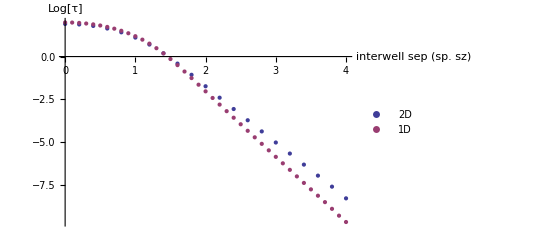

```mathematica
p2 = ListPlot[{TunnelingInterwell2D,TunnelingInterwellP1D},AxesLabel->{"interwell sep (sp. sz)","Log[τ]"},PlotLegends->{"2D","1D"}]
```

```mathematica
(*Show what happens as the depth is varied*)
```

```mathematica
TunnelingInterwell2DVaryV= Table[{b,Log[Tunneling2D[b,9,30,1]]},{b,5,20,.5}]
```

{{5.,0.70175},{5.5,0.764884},{6.,0.819999},{6.5,0.86886},{7.,0.912711},{7.5,0.952458},{8.,0.988783},{8.5,1.02222},{9.,1.05317},{9.5,1.08197},{10.,1.1089},{10.5,1.13418},{11.,1.15799},{11.5,1.18049},{12.,1.20181},{12.5,1.22206},{13.,1.24135},{13.5,1.25976},{14.,1.27736},{14.5,1.29422},{15.,1.3104},{15.5,1.32595},{16.,1.34092},{16.5,1.35534},{17.,1.36926},{17.5,1.3827},{18.,1.3957},{18.5,1.40829},{19.,1.42048},{19.5,1.43231},{20.,1.44379}}

```mathematica
TunnelingInterwellP1DVaryV=Table[{p,Log[computePlaneMatrix2Well[p,.5,.5,9,30][[1]][[2]]-computePlaneMatrix2Well[p,.5,.5,9,30][[1]][[1]]]},{p,5,20,.1}];
```

```mathematica
TunnelingInterwellP1D[[11]]
```

{1.,1.18983}

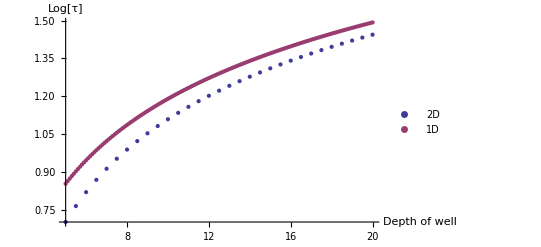

```mathematica
ListPlot[{TunnelingInterwell2DVaryV,TunnelingInterwellP1DVaryV},AxesLabel->{"Depth of well","Log[τ]"},PlotLegends->{"2D","1D"}]
```

```mathematica
Manipulate[ListPlot[Table[{p,Log[computePlaneMatrix2Well[p,.5,b,9,20][[1]][[2]]-computePlaneMatrix2Well[p,.5,b,9,20][[1]][[1]]]},{p,5,20,1}]],{b,0,3,.1}]
```

Part::partd: Part specification 5 ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 5 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification 6 ⟦ 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
(*Make a plot that shows this. As the depth gets bigger, I would expect all the values to approach each other*)
TunnelingVaryVVaryB = Table[{b/2.,Table[{V,Log[computePlaneMatrix2Well[V,.5,b/2.,12,200][[1]][[2]]-computePlaneMatrix2Well[V,.5,b/2.,12,200][[1]][[1]]]},{V,5,100,3}]},{b,{0,1,2,4,6}}];
```

```mathematica
Table[{p,computePlaneMatrix2Well[p,.5,.5,9,70][[1]][[2]]-computePlaneMatrix2Well[p,.5,.5,9,70][[1]][[1]]},{p,5,20,2}]
```

{{5,2.34764},{7,2.77935},{9,3.13097},{11,3.43165},{13,3.69657},{15,3.93475},{17,4.15207},{19,4.35255}}

```mathematica
TunnelingVaryVVaryB[[4]]
```

{2.,{{5,-6.26116},{8,-8.40093},{11,-10.2495},{14,-11.9},{17,-13.4053},{20,-14.7984},{23,-16.1021},{26,-17.3365},{29,-18.5405},{32,-19.9377},{35,-21.0021},{38,-19.6512},{41,-18.9697},{44,-18.4226},{47,-17.9223},{50,-17.4665},{53,-17.038},{56,-16.6392},{59,-16.2631},{62,-15.9081},{65,-15.5737},{68,-15.2563},{71,-14.955},{74,-14.6687},{77,-14.3956},{80,-14.1352},{83,-13.8862},{86,-13.6478},{89,-13.4193},{92,-13.2},{95,-12.9892},{98,-12.7865}}}

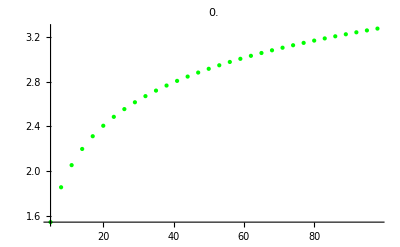
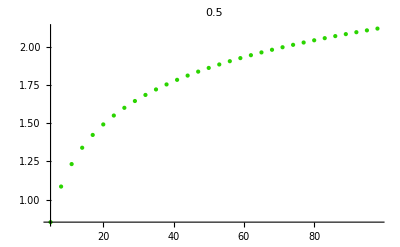
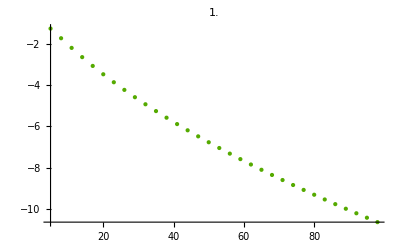
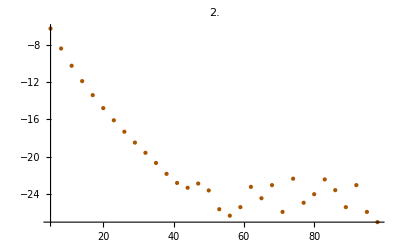
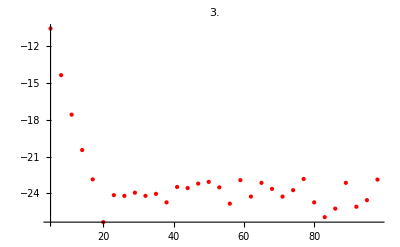

```mathematica
PlotListVVaryB=ListPlot[#[[2]],PlotLabel->#[[1]],PlotRange->All,PlotStyle->RGBColor[#1[[1]]/3.,(3-#1[[1]])/3,0]]&/@TunnelingVaryVVaryB
```

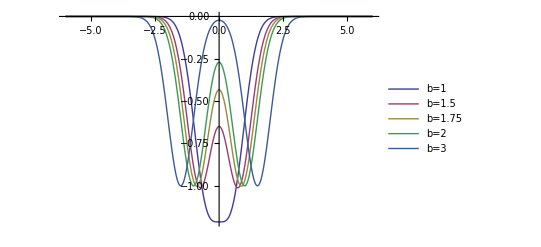

```mathematica
Plot[Evaluate[Table[-1*Exp[-2.*(x-b/2.)^2.]-1*Exp[-2.*(x+b/2.)^2.],{b,{1,1.5,1.75,2,3}}]],{x,-6,6},PlotLegends->{"b=1","b=1.5","b=1.75","b=2","b=3"}]
```

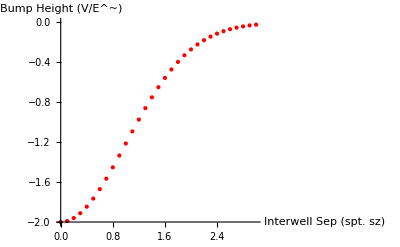

```mathematica
ListPlot[Table[{b,-1*Exp[-2.*(0-b/2.)^2.]-1*Exp[-2.*(0+b/2.)^2.]},{b,0,3,.1}],PlotStyle->Red,AxesLabel->{"Interwell Sep (spt. sz)","Bump Height (V/E^~)"}]
```

```mathematica
Manipulate[Plot[-V*Exp[-2.*(x-b/2.)^2.]-V*Exp[-2.*(x+b/2.)^2.],{x,-12,12},PlotRange->All],{V,0,100},{b,0,3}]
```

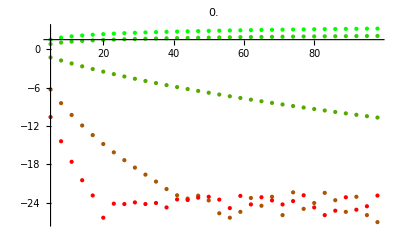

```mathematica
Show[PlotListVVaryB]
```

```mathematica
TunnelingVaryVVaryBver2 = Table[{b,Table[{V,Log[computePlaneMatrix2Well[V,.5,b/2.,10,200][[1]][[2]]-computePlaneMatrix2Well[V,.5,b/2.,10,200][[1]][[1]]]},{V,5,700,10}]},{b,{1,1.5,1.75,2,3}}];
```

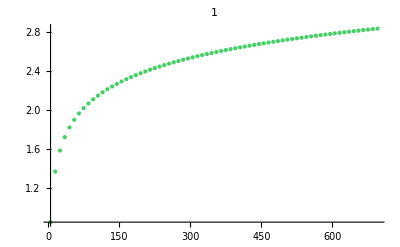
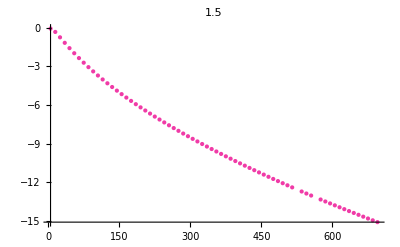
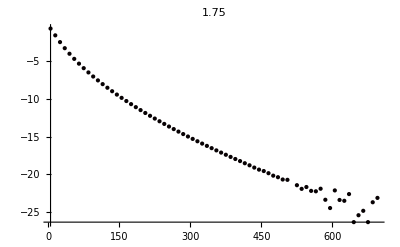
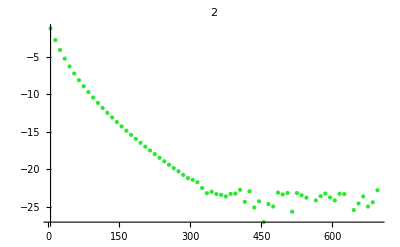
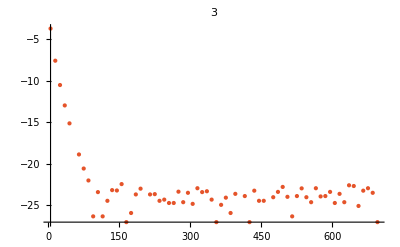

```mathematica
PlotListVVaryBver2=ListPlot[#[[2]],PlotLabel->#[[1]],PlotRange->All,PlotStyle->RGBColor[RandomReal[],RandomReal[],RandomReal[]]]&/@TunnelingVaryVVaryBver2
```

```mathematica
t1 = Transpose[TunnelingVaryVVaryBver2];
```

```mathematica
t1[[1]]
```

```mathematica
Export["tunnelingVandb.pdf",ListPlot[t1[[2]]/.{{x_,y_}->{x,Log[Exp[y/2.]]}}, PlotLegends->{t1[[1]]},AxesLabel->{"V/E~","Log[J/E^~]"}]]
```

tunnelingVandb.pdf

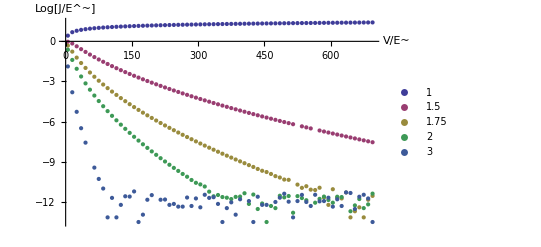

```mathematica
ListPlot[t1[[2]]/.{{x_,y_}->{x,Log[Exp[y/2.]]}}, PlotLegends->{t1[[1]]},AxesLabel->{"V/E~","Log[J/E^~]"}]
```

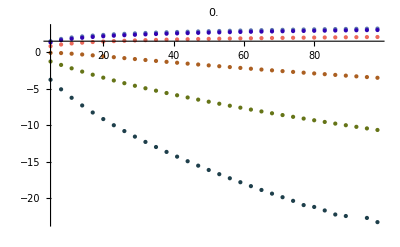

```mathematica
Show[PlotListVVaryBver2]
```

```mathematica
(*Testing adam's results*)
tun = (computePlaneMatrix2Well[Vkauf,.5,bkauf/2.,10,100][[1]][[2]]-computePlaneMatrix2Well[Vkauf,.5,bkauf/2.,10,100][[1]][[1]])
```

0.00571703

```mathematica
H=computePlaneMatrix2WellH[Vkauf,.5,bkauf/2.,10,8];
```

```mathematica
H[[1]][[1]]
```

-0.675823+0. ⅈ

```mathematica
(H[[1]][[1]] +2*Vkauf*Sqrt[π]*(Sqrt[2].5)/10)*206.76136213516995
```

653.009+0. ⅈ

67.4296

```mathematica
H[[1]][[2]]*206.76136213516995
```

-70724.7+0. ⅈ

```mathematica
Vkauf(Finf[bkauf/2.,.5,2*π/10,2*π/10*2,10]+Finf[-bkauf/2.,.5,2*π/10,2*π/10*2,10])*206.76136213516995
```

70724.7+0. ⅈ

```mathematica
Vkauf(Finf[bkauf/2.,.5,2*π/10*2,2*π/10,10]+Finf[-bkauf/2.,.5,2*π/10*2,2*π/10,10])*206.76136213516995
```

```mathematica
70800.49714673462-70158.35249699582
```

```mathematica
642.1446497387951
```

2017.36

```mathematica
49313.3330703053-47436.75149056868
```

1876.58

```mathematica
FourierCosSeries[
```

```mathematica
Vkauf(FL[bkauf/2.,.5,2*π/10,2*π/10*2,10]+FL[-bkauf/2.,.5,2*π/10,2*π/10*2,10])*206.76136213516995
```

75888.8+0. ⅈ

```mathematica
<<Units`
```

Tun::shdw: Symbol "Tun" appears in multiple contexts {"Units`", "Global`"}; definitions in context "Units`" may shadow or be shadowed by other definitions.

```mathematica
<<PhysicalConstants`
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
Convert[PlanckConstantReduced^2/(86.909 AtomicMassUnit*(750 Nano Meter)^2*PlanckConstant),Hertz]
```

206.757 Hertz

```mathematica
Vkauf=3162.5868653672755/206.76136213516995*100
```

1529.58

```mathematica
PlanckConstantReduced
```

1.05457×10^-34 Joule Second

```mathematica
1.056^2/
```

```mathematica
bkauf=.9/.75
```

1.2

```mathematica
PlanckConstant
```

6.62607×10^-34 Joule Second

```mathematica
2*π*PlanckConstantReduced
```

6.62607×10^-34 Joule Second

```mathematica
Convert[87 AtomicMassUnit,Kilogram]
```

1.44467×10^-25 Kilogram

```mathematica
Integrate[Cos[(l-m)*x]*Exp[-2*(x-bsep)^2/□
```

```mathematica
computePlaneMatrix2WellBox
```

```mathematica
(*Testing adam's results*)
tun = (computePlaneMatrix2WellBox[Vkauf,.5,bkauf/2.,12,100][[1]][[2]]-computePlaneMatrix2WellBox[Vkauf,.5,bkauf/2.,12,100][[1]][[1]])
```

19.2424

```mathematica
(*Get another graph for adam's tunneling depth as a function of the interwell seperation*)
```

```mathematica
tunv1 = Table[(computePlaneMatrix2Well[Vkauf,.5,b/2.,10,100][[1]][[2]]-computePlaneMatrix2Well[Vkauf,.5,b/2.,10,100][[1]][[1]]),{b,1,2,.1}]
```

{22.3503,1.9253,0.00574624,0.0000183897,0.00013695,0.000211465,0.000177874,0.000111886,0.0000518335,6.01005×10^-6,0.0000277157}

```mathematica
tunv200 = Table[{b,(computePlaneMatrix2Well[Vkauf,.5,b/2.,10,200][[1]][[2]]-computePlaneMatrix2Well[Vkauf,.5,b/2.,10,200][[1]][[1]])},{b,1,2,.1}]
```

{{1.,22.3503},{1.1,1.9253},{1.2,0.005731},{1.3,8.20827×10^-6},{1.4,1.16179×10^-8},{1.5,1.81899×10^-11},{1.6,7.09406×10^-11},{1.7,4.91127×10^-11},{1.8,8.18545×10^-11},{1.9,4.54747×10^-11},{2.,1.81899×10^-11}}

```mathematica
tunv2 = Table[{b,(computePlaneMatrix2Well[Vkauf,.5,b/2.,10,300][[1]][[2]]-computePlaneMatrix2Well[Vkauf,.5,b/2.,10,300][[1]][[1]])},{b,1,2,.1}]
```

{{1.,22.3503},{1.1,1.9253},{1.2,0.005731},{1.3,8.20829×10^-6},{1.4,1.16088×10^-8},{1.5,6.18456×10^-11},{1.6,7.09406×10^-11},{1.7,8.54925×10^-11},{1.8,7.27596×10^-12+4.98295×10^-13 ⅈ},{1.9,8.73115×10^-11},{2.,8.00355×10^-11}}

```mathematica
(*200 Seems converged)*)
```

```mathematica
tunv2/.{{x_,y_}->{x,Log[y]}}
```

{{1.,3.10684},{1.1,0.655083},{1.2,-5.16187},{1.3,-11.7104},{1.4,-18.2715},{1.5,-23.5064},{1.6,-23.3692},{1.7,-23.1826},{1.8,-25.6441+0.0683784 ⅈ},{1.9,-23.1615},{2.,-23.2486}}

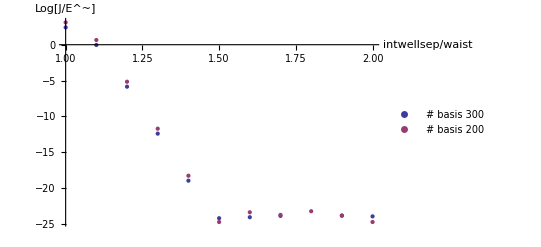

```mathematica
tunnelinginterwellplot =ListPlot[{tunv2/.{{x_,y_}->{x,Log[y/2.]}},tunv200/.{{x_,y_}->{x,Log[y]}}}, PlotLegends->{"# basis 300","# basis 200"},AxesLabel->{"intwellsep/waist","Log[J/E^~]"}]
```

```mathematica
Export["tunvbplt.pdf",tunnelinginterwellplot]
```

tunvbplt.pdf

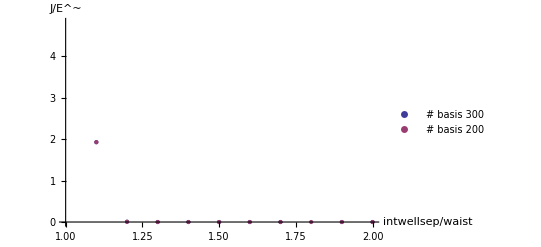

```mathematica
tunnelinginterwellplotnolog =ListPlot[{tunv2,tunv200}, PlotLegends->{"# basis 300","# basis 200"},AxesLabel->{"intwellsep/waist","J/E^~"}]
```

```mathematica
tunv200zoom = Table[{b,(computePlaneMatrix2Well[Vkauf,.5,b/2.,10,200][[1]][[2]]-computePlaneMatrix2Well[Vkauf,.5,b/2.,10,200][[1]][[1]])},{b,1,1.3,.01}]
```

{{1.,22.3503},{1.01,20.0601},{1.02,17.7145},{1.03,15.3292},{1.04,12.9323},{1.05,10.5693},{1.06,8.30717},{1.07,6.23314},{1.08,4.44005},{1.09,2.99793},{1.1,1.9253},{1.11,1.18444},{1.12,0.70375},{1.13,0.4068},{1.14,0.230088},{1.15,0.12789+1.64735×10^-22 ⅈ},{1.16,0.0700854},{1.17,0.0379634},{1.18,0.0203668},{1.19,0.0108396+1.45926×10^-16 ⅈ},{1.2,0.005731},{1.21,0.00301351},{1.22,0.00157749},{1.23,0.000822766},{1.24,0.000427879},{1.25,0.000222012},{1.26,0.000114996},{1.27,0.0000594904},{1.28,0.000030751},{1.29,0.0000158884},{1.3,8.20827×10^-6}}

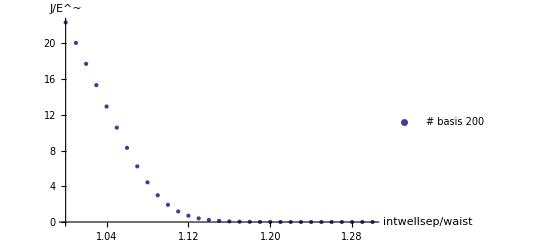

```mathematica
tunnelinginterwellplotzoom =ListPlot[tunv200zoom ,PlotLegends->{"# basis 200"},AxesLabel->{"intwellsep/waist","J/E^~"}]
```

```mathematica
Export["tunvbpltzoom.pdf",tunnelinginterwellplotzoom]
```

tunvbpltzoom.pdf

## Functions:

```mathematica
Clear[h]
Clear[M]
h = 1.05457173*10^-34;
M = 1.443161*10^-25;
```

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
H2p[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x+b)^2+y^2))/c^2]Φ[n,x,m,y,L]-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
HPlanebtest[V_,L_,n_,m_,l_,q_,b_]:= 
(*I had some trouble getting the factors in EXp right, but this configuration worked. This is for one well only! This is the generalizating of HPlane, which doesn't worry about b. This basically lets me offset my one well wherever I want to double check that I have the right form of the analytics*)KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ(2*π/L)(m-q))^2/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]-V*Exp[((-2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]//N
```

```mathematica
HMatrix[V_,L_,size_]:=ArrayFlatten[Table[HPlane[V,L,m,l,n,q],{m,-size,size},{n,-size,size},{l,-size,size},{q,-size,size}]//N]
```

```mathematica
groundState[EM_,L_,x_,y_]:=Compile[{Size=Sqrt[Length[EM]], i,j},
(*Given an eigenvector, this will compute a plottable version of the wavefunction. However, there is little sophistication, the user must still change the index conversion number by hand.

Note: there was a problem: use ky for calculating the number on x and y, as the kx function gives the row of a matrix, but, for the eigenvector, it is just a 'column' vector, so just use ky*) Sum[Normalize[EM][[(i-1)*Size+j]]*N[Exp[-ⅈ*2.*π/L*(ky[i,Size]*x+ky[j,Size]*y)]/L,8],{i,1,Size},{j,1,Size}]]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix//N]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

Harmonic Oscillator Functions:
HMV1[1,2,.1,0,.5]

```mathematica
HMV1[1,1,.1,0,0.5]
```

0.0103913

```mathematica
HMV1[1,2,0.1,0.5]
```

HMV1[1,2,0.1,0.5]

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[(2V)/c^2]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{m,0,size-1},{l,0,size-1},{q,0,size-1}]]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Compile[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4.*V*c^2)]//N},{x,-10,10}]
]
```

```mathematica
plotGround
```

plotGround

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis,Em},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,-b,c]*HMV1[l,q,ω,b,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/c^2],x,y},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
EnGround2wellHO[V_,b_,c_,size_]:=EnGround2wellHO[V,b,c,size]= Module[{Em,M},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigenvalues[M])
]
```

### Sparse Matrices Stuff:

```mathematica
R[deltaK_,L_]:=R[deltaK]=Exp[(-(2*π/L)^2(deltaK)^2)/8.]//N
```

```mathematica
yIndex[i_,size_] =Mod[i,size,1]
```

Mod[i,size,1]

```mathematica
(*y index will take a number from 1-n, and convert it into a quantum number for ky. This will be an integer starting from -p..p.*)
```

```mathematica
yIndex[2,4]
```

2

```mathematica
ky[i_,size_]=yIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+Mod[i,size,1]

```mathematica
(*this will convert our index number to a range that runs over negative numbers so we can get backwards waves*)
```

```mathematica
kx[i_,size_]=xIndex[i,size]-(size-1)/2-1
```

(1-size)/2+(i-Mod[i,size,1])/size

```mathematica
kx[6,5]
```

-1

```mathematica
xIndex[i_,size_]=(i-Mod[i,size,1])/size+1
```

1+(i-Mod[i,size,1])/size

```mathematica
BuildPlaneMatrix[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
BuildPlaneMatrix2D2Well[V_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->(R2W[kx[j,p]-kx[i,p],L,b]+R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
R2W[deltaK_,L_,b_]:=R2W[deltaK,L,b]=Exp[((2.*b+ⅈ(2.*π/L)(deltaK)/2)^2-4.*b^2)/2.]//N
```

```mathematica
(*Tunneling for a 2D 2Well case*)
Tunneling2DWellListGen[basisnum_]:=
(*Need to double check that L=1 is okay for small b*)Module[{EnergyList,TunnelingList},
EnergyList= Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,basisnum,b/2.]-1000.*IdentityMatrix[basisnum^2],2]+1000},{b,.1,4,.2}];

TunnelingList= Table[{EnergyList[[p]][[1]],EnergyList[[p]][[2]][[2]]-EnergyList[[p]][[2]][[1]]},{p,1,Length[EnergyList]}]
]
```

```mathematica
10/25.
```

0.4

```mathematica
(*1D Functions for plane waves*)
```

```mathematica
computePlaneMatrix2WellH[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]

]
```

```mathematica
computePlaneMatrix2WellBox[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - 1/2(V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[1/(2 c^2)(-b+ⅈ*c^2(m-l))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length)-1/2(V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length+V*Exp[(1/(2 c^2)(b+ⅈ*c^2(m-l))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length);
M = Eigensystem[Table[H[π*l/length,π*m/length],{l,1,p},{m,1,p}]-10000*IdentityMatrix[p],3]

]
```

```mathematica
ComputePlaneWaveEN[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M,EM},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag;

EM = Eigenvalues[M-10000*IdentityMatrix[p^2],3]
]
```

```mathematica
(-bsep+ⅈ*c^2(l-m))^2//Expand
```

bsep^2-2 ⅈ bsep c^2 l-c^4 l^2+2 ⅈ bsep c^2 m+2 c^4 l m-c^4 m^2

```mathematica
1/2 (k-l) (2 ⅈ bsep+(-k+l) w^2)//Expand
```

ⅈ bsep k-ⅈ bsep l-(k^2 w^2)/2+k l w^2-(l^2 w^2)/2

```mathematica
Tunneling2D[V_,L_,p_,b_]:= Module[{En0,En1, EnList,T},
EnList = Eigenvalues[BuildPlaneMatrix2D2Well[V,L,p,b/2.]-1000.*IdentityMatrix[p^2],2]+1000;
En1 = EnList[[2]];
En0  =EnList [[1]];
T = En1-En0
]
```

```mathematica
Tunneling2D[10,9,15,.1]
```

6.80681

```mathematica
Tunneling2D[10,8,30,0]
```

6.71513

```mathematica
Tunneling2DWellListGen[15]
```

{{0.1,6.80681},{0.3,6.40604},{0.5,5.66045},{0.7,4.67193},{0.9,3.57173},{1.1,2.50163},{1.3,1.59078},{1.5,0.918494},{1.7,0.485276},{1.9,0.239587},{2.1,0.120797},{2.3,0.071051},{2.5,0.0439555},{2.7,0.0190089},{2.9,0.000724249},{3.1,0.00189499},{3.3,0.00636673},{3.5,0.010486},{3.7,0.00319497},{3.9,0.00679268}}

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000*IdentityMatrix[p+1],3]

]
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-1000000*IdentityMatrix[p+1],3]

]
```